# Math 223: Homework 8

Maia Powell

2 April 2021

## Problem 1

#### Find the asymptotic behavior of (∫_0)^2(sin(t) + t)e^ixt dt as x→ +∞ up to terms involving 1/x^2.

We first observe that ϕ(t)=t is monotonic in [0,2], and sin(t)+t is smooth. 

Following the formula 
I(x) = ∫_a^b f(t) ⅇ^(ⅈ x t)ⅆt∼ ∑_(n=0)^∞ (-1)^n/(ⅈ x)^(n+1)[f^(n)(b) ⅇ^(ⅈ x b)-f^(n)(a) ⅇ^(ⅈ x a)],
we obtain: 
n=0:
	1/ix[(sin(2)+2)e^(2ix)] 
n=1:
	1/x^2[(cos(2)+1)e^(2ix)- (cos(0))]
	
Thus, we approximate that I(x) ~ 1/ix[(sin(2)+2)e^(2ix)] +1/x^2[(cos(2)+1)e^(2ix)- 1]

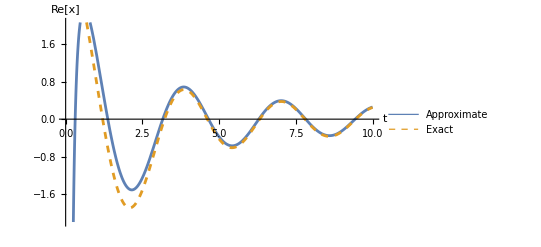

```mathematica
Plot[{Re[1/(ⅈ*x)(Sin[2]+2)ⅇ^(2ⅈ*x)]+Re[1/x^2((Cos[2]+1)ⅇ^(2ⅈ*x)-Cos[0])], Re[NIntegrate[((Sin[t])+t)ⅇ^(ⅈ*x*t), {t,0,2}]]},{x,0,10},PlotStyle-> {Directive[Solid,Thickness[0.005]], Directive[Dashed,Thickness[0.005]]},AxesLabel->{Style["t",Italic,18],Style["Re[x]", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Approximate","Exact"}]
```

## Problem 2

#### Using the method of stationary phase to find the leading behaviors of the following integrals as x→ +∞.

(a.) (∫_0)^1 tan(t)e^(ixt^4)dt

Because tan(t) ~ t, we would like to approximate ∫_0^1 tan(t) ⅇ^(ⅈ x t^4)dt  as ∫_0^1 t ⅇ^(ⅈ x t^4)dt.

We first perform a substitution, such that u=t^2:
∫_0^1 t ⅇ^(ⅈ x t^4)dt = ∫_0^1 1/2 ⅇ^(ⅈ x t^2)dt

We then use the method of stationary phase with f(t) = 1/2 and ϕ(t) = t^2 → ϕ''(t)=2. Setting ϕ'(t) = 2t=0, we obtain that t* = 0 = a.  Thus, using the formula I(x) ∼ 1/2((2π)/(x|ϕ''(a)|))^(1/2)f(a) ⅇ^(ⅈ x ϕ(a)+ⅈ π sgn(ϕ''(a))/4), we obtain:
I(x) ∼ 1/2(π/x)^(1/2)1/2 ⅇ^(ⅈ π /4)

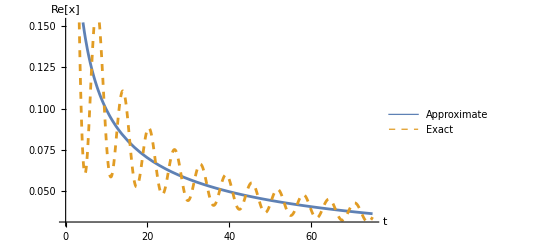

```mathematica
Plot[{Re[1/2(π/x)^(1/2)1/2 ⅇ^(ⅈ π /4)], Re[NIntegrate[Tan[t] ⅇ^(ⅈ x* t^4), {t,0,1}]]},{x,0,75},PlotStyle-> {Directive[Solid,Thickness[0.005]], Directive[Dashed,Thickness[0.005]]},AxesLabel->{Style["t",Italic,18],Style["Re[x]", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Approximate","Exact"}]
```

(b.) (∫_(1/2))^2(1+t)e^(ix(t^3/3-t))dt

We will use the method of stationary phase with f(t) = 1+t and ϕ(t) = t^3/3-t → ϕ''(t)=2t. Setting ϕ'(t) = t^2-1= 0, we obtain that (t^*)_1 = -1 and (t^*)_2 = 1 . We observe that only (t^*)_2 = 1 is within our interval, thus a=1. Using the formula I(x) ∼ ((2π)/(x|ϕ''(a)|))^(1/2)f(a) ⅇ^(ⅈ x ϕ(a)+ⅈ π sgn(ϕ''(a))/4), we obtain:
I(x) ∼ 2(π/x)^(1/2) ⅇ^((-2ⅈ x)/3+ⅈ π /4)

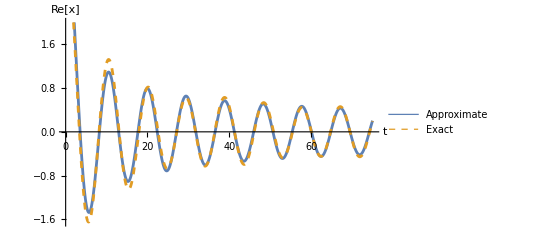

```mathematica
Plot[{Re[2(π/x)^(1/2) ⅇ^((-2ⅈ x)/3+ⅈ π /4)], Re[NIntegrate[(1+t) ⅇ^(ⅈ x*(t^3/3-t)), {t,1/2,2}]]},{x,0,75},PlotStyle-> {Directive[Solid,Thickness[0.005]], Directive[Dashed,Thickness[0.005]]},AxesLabel->{Style["t",Italic,18],Style["Re[x]", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"Approximate","Exact"}]
```